# Quantum Information Theory

```mathematica
Quit[]
```

```mathematica
Needs["QuantumMob`Q3`"]
```

```mathematica
Let[Qubit,S]
```

"Table of Contents"

## Shannon Entropy

### Definition

Let us consider a binary distribution.

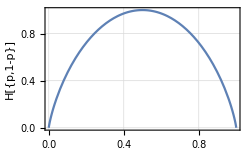

```mathematica
Plot[ShannonEntropy[{p,1-p}],{p,0,1},FrameLabel->{"p","H[{p,1-p}]"}]
```

### Relative Entropy

### Mutual Information

### Data Compression

### Communication over Noisy Channel

## Von Neumann Entropy

### Definition

We consider a simple example. The density operator describes an ensemble of two pure states 0 and +:=(0+1)/√2.

```mathematica
vec=(Ket[S->0]+Ket[S->1])/Sqrt[2]
rho=p*Dyad[Ket[],Ket[],S]+(1-p)*Dyad[vec,vec,S]
Matrix[rho]//MatrixForm
```

(0_S+1_S)/(√2)

p 0_S0_S+(1-p) ((0_S0_S)/2+(0_S1_S)/2+(1_S0_S)/2+(1_S1_S)/2)

(1/2+p/2 | 1/2-p/2
1/2-p/2 | 1/2-p/2)

Here are the eigenvalues of the density operator.

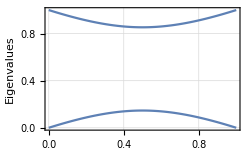

```mathematica
Plot[ProperValues[rho],{p,0,1},FrameLabel->{"p","Eigenvalues"}]
```

Here is the von Neumann entropy of the density operator as a function of p.

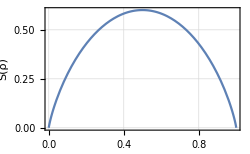

```mathematica
Plot[VonNeumannEntropy[rho],{p,0,1},FrameLabel->{"p","S(ρ)"}]
```

As another example, we consider a interpolation between the completely random state I/2 and a pure state (I+ a·S)/2 with ∥a∥=1.

```mathematica
rho=1/2+(1-p){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}.S[All]/2
Tr[Matrix[rho]]//Simplify
```

1/2+1/2 (1-p) (Cos[θ] S^z+Cos[ϕ] S^x Sin[θ]+S^y Sin[θ] Sin[ϕ])

1

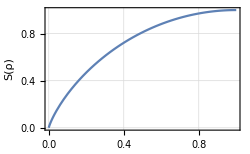

```mathematica
Block[{θ=Pi/3,ϕ=Pi/6},Plot[VonNeumannEntropy[rho],{p,0,1},FrameLabel->{"p","S(ρ)"}]]
```

### Relative Entropy

Consider a quantum state described by the following density operator.

```mathematica
rho=1/2+S[3]/4;
rho//Matrix//MatrixForm
```

(3/4 | 0
0 | 1/4)

Here is the von Neumann entropy of the above state.

```mathematica
VonNeumannEntropy[rho]
```

1/2+(3 Log[4/3])/(4 Log[2])

Consider another density operator.

```mathematica
sig=S[6]**rho**S[6];
sig//Matrix//MatrixForm
```

(1/2 | 1/4
1/4 | 1/2)

It has the same eigenvalues as rho and hence the same von Neumann entropy.

```mathematica
VonNeumannEntropy[sig]
```

1/2+(3 Log[4/3])/(4 Log[2])

This gives the relative entropy of rho to sig.

```mathematica
VonNeumannEntropy[rho,sig]
```

1/2-Log[4/3]/(4 Log[2])

### Properties of Von Neumann Entropy

## Entanglement and Entropy

### What is Entanglement?

### Separability Tests

We consider a Werner state, and apply the positive partial transposition criterion.

We first prepare a singlet state.

```mathematica
singlet=(Ket[S[2]->1]-Ket[S[1]->1])/Sqrt[2]//KetRegulate
```

(0_S_11_S_2-1_S_10_S_2)/(√2)

A Werner state is a convex linear superposition of the single state and the completely random mixture.

```mathematica
rho=p*Dyad[singlet,singlet,S@{1,2}]+(1-p)/4//Elaborate
rho//Matrix//MatrixForm
```

1/4-1/4 p S_1^xS_2^x-1/4 p S_1^yS_2^y-1/4 p S_1^zS_2^z

(1/4-p/4 | 0 | 0 | 0
0 | 1/4+p/4 | -p/2 | 0
0 | -p/2 | 1/4+p/4 | 0
0 | 0 | 0 | 1/4-p/4)

This is the partial transposition of rho with respect to the second qubit.

```mathematica
new=PartialTranspose[rho,S[2]]//Elaborate
new//Matrix//MatrixForm
```

1/4-1/4 p S_1^xS_2^x+1/4 p S_1^yS_2^y-1/4 p S_1^zS_2^z

(1/4-p/4 | 0 | 0 | -p/2
0 | 1/4+p/4 | 0 | 0
0 | 0 | 1/4+p/4 | 0
-p/2 | 0 | 0 | 1/4-p/4)

This shows the eigenvalues of the partial transposition of rho. For p<1/3, all eigenvalues are positive and the positive partial transposition is satisfied. However, two of the eigenvalues get negative for p>1/3, and hence the state must be entangled.

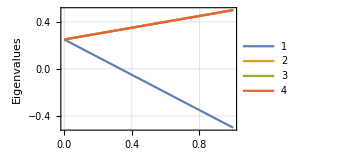

```mathematica
Plot[Evaluate@ProperValues[new],{p,0,1},FrameLabel->{"p","Eigenvalues"},PlotLegends->Automatic]
```

We apply the positive partial transposition criterion to another example. Again, we first prepare the singlet state.

```mathematica
singlet=(Ket[S[2]->1]-Ket[S[1]->1])/Sqrt[2]//KetRegulate
```

(0_S_11_S_2-1_S_10_S_2)/(√2)

The state we are concerned with is a mixture of the singlet state and a fully polarized state, pSS+(1-p)0000.

```mathematica
rho=p*Dyad[singlet,singlet,S@{1,2}]+(1-p)Dyad[Ket[],Ket[],S@{1,2}]//Elaborate
rho//Matrix//Simplify//MatrixForm
```

1/4-1/4 p S_1^xS_2^x-1/4 p S_1^yS_2^y+1/4 (1-2 p) S_1^zS_2^z+1/4 (1-p) S_1^z+1/4 (1-p) S_2^z

(1-p | 0 | 0 | 0
0 | p/2 | -p/2 | 0
0 | -p/2 | p/2 | 0
0 | 0 | 0 | 0)

This is the partial transposition of rho with respect to the second qubit.

```mathematica
new=PartialTranspose[rho,S[2]]//Elaborate
new//Matrix//Simplify//MatrixForm
```

1/4-1/4 p S_1^xS_2^x+1/4 p S_1^yS_2^y+1/4 (1-2 p) S_1^zS_2^z+1/4 (1-p) S_1^z+1/4 (1-p) S_2^z

(1-p | 0 | 0 | -p/2
0 | p/2 | 0 | 0
0 | 0 | p/2 | 0
-p/2 | 0 | 0 | 0)

This shows that for all 0<p≤1, the partial transposition has a negative eigenvalue. Therefore, the state must be entangled.

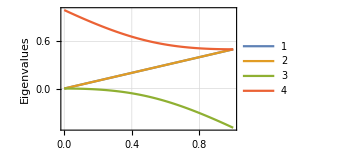

```mathematica
Plot[Evaluate@ProperValues[new],{p,0,1},FrameLabel->{"p","Eigenvalues"},PlotLegends->Automatic]
```

### Entanglement Distillation

### Entanglement Measures

The entanglement measures for mixed states enable to investigate multi-partite entanglement. As an example, we consider the control and target registers each of which is consisting of n qubits and use the logarithmic negativity to characterize the multi-partite entanglement in the system.

```mathematica
$n=2;
cc=Range[$n];
tt=$n+cc;
```

We generate a quantum state with a maximally entanglement between the control and target registers.

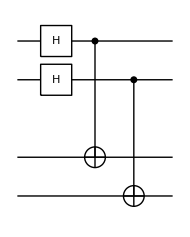

```mathematica
qc=QuantumCircuit[S[cc,6],
Sequence@@MapThread[CNOT,{S[cc],S[tt]}],
"Invisible"->S[$n+1/2]]
```

This is the desired state.

```mathematica
out=qc**Ket[]
```

1/2 0_S_10_S_20_S_30_S_4+1/2 0_S_11_S_20_S_31_S_4+1/2 1_S_10_S_21_S_30_S_4+1/2 1_S_11_S_21_S_31_S_4

Note that even through the state exhibits a maximal entanglement between the control and target registers, it is product state between two registers respectively containing qubits 1 and 3 and qubits 2 and 4.

```mathematica
KetFactor[out]
```

1/2 (0_S_10_S_3+1_S_11_S_3)⊗(0_S_20_S_4+1_S_21_S_4)

Keeping in mind the above fact, we examine a mixed state of the control register that has been obtained by tracing out the target register.

```mathematica
rho12=PartialTrace[out,S@tt]
PauliForm[rho12,S@{1,2}]
```

1/4

(I⊗I)/4

We expect no entanglement between two qubits 1 and 2. Indeed, it is confirmed by the following evaluation.

```mathematica
LogarithmicNegativity[rho12,S[1],S[2]]
```

0

Next, we consider the mixed state of qubits 1 and 3 that results from tracing out qubits 2 and 4.

```mathematica
rho13=PartialTrace[out,S@{2,4}]//Elaborate
```

1/4+1/4 S_1^xS_3^x-1/4 S_1^yS_3^y+1/4 S_1^zS_3^z

We expect an entanglement to some extent, and this shows that it is the case.

```mathematica
LogarithmicNegativity[rho13,S@{1,3},S[3]]
```

1